## Constrained 1d optimal control (Prob. 7.15 / Ex. 7.5)

```mathematica
Clear["Global`*"];
```

Optimal control problem has running cost    L=1/2(x^2+u^2)    integrated over t ∈(0,∞).  
Eq. of motion is        xdot = -x + u,     x(0) = x0.

Unconstrained case (leads to u(t) = -K* x(t), with K* = √2-1.

```mathematica
j[τ_,xτ_]:=Module[{eq,init,x,λ,t,xs,λs,us,hs},
eq={
x'[t]==- x[t]-λ[t], 
λ'[t]==  λ[t]-x[t]
};
init={x[τ]==xτ,λ[∞]==0};
{xs,λs}=DSolveValue[{eq,init},{x,λ},t]//FullSimplify;
us[t_]:=-λs[t];
hs[t_]:=1/2(xs[t]-λs[t])^2-λs[t]^2//FullSimplify;
{xs,λs,us,hs}]
{xu,λu,uu,hu}=j[τ,xτ];
Grid[{{
xu[t],Kstar=uu[t]/(-xu[t])//FullSimplify
}},Spacings->4]
```

DSolveValue::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Set::shape: Lists {xs$1226823,λs$1226823} and DSolveValue[{{x$1226823'[t$1226823]==-x$1226823[t$1226823]-λ$1226823[t$1226823],λ$1226823'[t$1226823]==-x$1226823[t$1226823]+λ$1226823[t$1226823]},{x$1226823[τ]==xτ,λ$1226823[∞]==0}},{x$1226823,λ$1226823},t$1226823] are not the same shape.

xs$1226823[t] | λs$1226823[t]/xs$1226823[t]

```mathematica
Plot[{xu[t],λu[t],uu[t]}/.{τ->1,xτ->1},{t,0,10},PlotRange->All]
```

-Graphics-

Constrained case

```mathematica
jc[τ_,x0_]:=Module[{eqx,initx,eqλ,initλ,x,λ,t,xs,λs,us,hs},
eqx=x'[t]==- x[t]-1;
initx=x[0]==x0;
xs=DSolveValue[{eqx,initx},x,t];

eqλ=λ'[t]==  λ[t]-xs[t];
initλ=λ[τ]==(√2-1)xs[τ];  (* wrong condition??  λ not continuous ?  *)
λs=DSolveValue[{eqλ,initλ},λ,t]//FullSimplify;

us[t_]:=-1;
hs[t_]:=1/2(xs[t]^2+1)-λs[t]xs[t]-λs[t]//FullSimplify;
{xs,λs,us,hs}]
{xc,λc,uc,hc}=jc[τ,x0];
{xc[t],λc[t],uc[t],hc[t]}  (* solution for λ(t) is probably wrong, since final condition may be wrong, but important part is ok *)
```

{-ⅇ^-t (-1+ⅇ^t-x0),-1/2 ⅇ^(-t-2 τ) (3 ⅇ^(2 t)-2 √2 ⅇ^(2 t)-ⅇ^(2 τ)-4 ⅇ^(2 t+τ)+2 √2 ⅇ^(2 t+τ)+2 ⅇ^(t+2 τ)+3 ⅇ^(2 t) x0-2 √2 ⅇ^(2 t) x0-ⅇ^(2 τ) x0),-1,1+1/2 ⅇ^(-2 τ) (1+x0) (2 (-2+√2) ⅇ^τ-(-3+2 √2) (1+x0))}

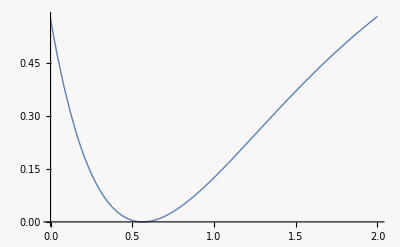

```mathematica
hc1=hc[t]/.x0->5;
Plot[hc1,{τ,0,2}]
```

```mathematica
FindMinimum[hc1,{τ,1}]
```

{-6.66134×10^-16,{τ→0.563812}}

```mathematica
FindRoot[hc1,{τ,1}]
```

{τ→0.563812}

Compute overall cost function jtot

```mathematica
j1[τ_]:=Integrate[1/2 xc[t]^2,{t,0,τ}]+τ/2//FullSimplify;j1[τ]
```

1/4 (-3+(-2+x0) x0+4 ⅇ^-τ (1+x0)-ⅇ^(-2 τ) (1+x0)^2+4 τ)

```mathematica
1/2(1+(-1+√2)^2)//Simplify
```

2-√2

```mathematica
xc[τ]
```

-ⅇ^-τ (-1+ⅇ^τ-x0)

```mathematica
j2[τ_]:=Integrate[(2-√2)xu[t]^2/.xτ->xc[τ],{t,τ,∞}]//Simplify;  j2[τ]
```

∫_τ^∞ -((-2+√2) xs$1226823[t]^2)ⅆt

```mathematica
jtot[τ_]:=j1[τ]+j2[τ]//Simplify;jtot[τ]
```

-3/4+1/4 (-2+x0) x0+ⅇ^-τ (1+x0)-1/4 ⅇ^(-2 τ) (1+x0)^2+τ+∫_τ^∞ -((-2+√2) xs$1226823[t]^2)ⅆt

```mathematica
jtot1=jtot[τ]/.x0->5//FullSimplify
```

3+ⅇ^(-2 τ) (-9+6 ⅇ^τ)+τ+∫_τ^∞ -((-2+√2) xs$1226823[t]^2)ⅆt

```mathematica
Grid[{{Plot[jtot1,{τ,0.55,0.58}],Log[(1+5)/(2+√2)]//N,FindMinimum[{jtot1,τ≥0.5},{τ,1}]}},Spacings->2]
```

NIntegrate::inumr: The integrand -((-2+√2) xs$1226823[t]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.550001}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::nrnum: The function value 4.98926+∫_1.^∞ -((-2+√2) xs$1226823[t]^2)ⅆt is not a real number at {τ} = {1.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMinimum::nrnum: The function value 4.98925+∫_0.999994^∞ -((-2+√2) xs$1226823[t]^2)ⅆt is not a real number at {τ} = {0.999994}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[3+ⅇ^(-2 τ) (-9+6 Power[«2»])+τ+∫_τ^∞ -((-2+Power[«2»]) xs$1226823[«1»]^2)ⅆt],Block},{0,{{{},1,0,Hold[τ],0,0}}},{{{1,1,817},{«1»,«1»}}},«1»,{904,MachinePrecision,{{Automatic},{Hold[3+Power[«2»] Plus[«2»]+τ+Integrate[Times[«3»],{«3»}]],Block}},True,{«1»},FindMinimum,Automatic,None},{None,None,None}] failed at {1.}.

-Graphics- | 0.563812 | FindMinimum[{jtot1,τ≥0.5},{τ,1}]

```mathematica
Simplify/@{D[jtot1, τ], D[jtot1, τ]/.τ->Log[(1+5)/(2+√2)]}  (* check the minimization *)
```

{1+18 ⅇ^(-2 τ)-6 ⅇ^-τ+(-2+√2) xs$1226823[τ]^2,2+√2+(-2+√2) xs$1226823[Log[6-3 √2]]^2}

So the minimum (inflection pt., actually) occurs just at the crossover point where u=-1, as one might expect.

Now do it numerically the “right” way, with a single equation, using u = -Clip[λ].  Unfortunately, as DSolveValue does not seem to work with the piecewise ODE (although it claims it can...), I do it numerically.  But the numerical solution confirms the above analysis.

```mathematica
j3[x0_]:=Module[{eq,init,x,λ,t,xs,λs,us,τ},
τ=10;
eq={
x'[t]==- x[t]-Clip[λ[t]],   (* value between ±1 *)
λ'[t]==  λ[t]-x[t]
};
init={x[0]==x0,λ[τ]==0};
{xs,λs}=NDSolveValue[{eq,init},{x,λ},{t,0,τ}]//FullSimplify;
us[t_]:=-Clip[λs[t]];
{xs,λs,us}]
{x,λ,u}=j3[5];
```

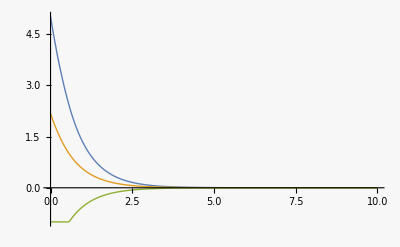

```mathematica
Plot[{x[t],λ[t],u[t]},{t,0,10},PlotRange->All]
```

```mathematica
hc[τ]/.τ->Log[(1+x0)/(2+√2)]//Simplify
```

0

```mathematica
(3/2-√2)(2+√2)^2//Simplify
```

1